## Symmedial Triangle: Orbit and Excentral

```mathematica
Clear@symmedialCircle;
symmedialCircle[tri_,sides_]:=Module[{center,radius,symTri,R},
R=getCircumradius@sides;
symTri=symmedialTriangle[tri,sides];
center=getCircumcenter@@symTri;
radius=magn[symTri[[1]]-center];
{center,radius}];
```

```mathematica
DynamicModule[{symLocus,a=1.5,ell,o,n,s,exc,symCirCtr,symCirRad,symCirCtrExc,symCirRadExc,gr},
symLocus=symmedianLocus[a,2π];
Manipulate[
{o,n,s}=orbitNormals[a,toRad@tDeg];
{symCirCtr,symCirRad}=symmedialCircle[o,s];
exc=excentralTriangle[o,s];
{symCirCtrExc,symCirRadExc}=symmedialCircle[exc,triLengthsRL@exc];
gr=Graphics[{PointSize@Medium,
{"sym"/.ptClrs,Circle[symCirCtr,symCirRad],Point@symCirCtr},
{"exc"/.ptClrs,Circle[symCirCtrExc,symCirRadExc],Point@symCirCtrExc}
}];
Show[{drawSimT[a,toRad@tDeg,drNotables->True],symLocus,gr},
PlotRange->{{-a,a},{-1.1,1.1}},
ImageSize->600],
{{tDeg,30},-180,180,1}]]
```

Set::shape: Lists {FE`symCirCtr$$97, FE`symCirRad$$97} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$97, FE`symCirRadExc$$97} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$97, FE`symCirRad$$97} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$97, FE`symCirRadExc$$97} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{safeDiv[-2.79996, 1.64253], safeDiv[-3.45142, 1.64253]}, {safeDiv[-1.27239, 1.07792], safeDiv[3.62506, 1.07792]}, {safeDiv[7.89096, 4.01706], safeDiv[-1.07757, 4.01706]}}, {√(-safeDiv[« 2 »] + safeDiv[3.62506, 1.07792])^2 + (« 1 »)^2, √(-safeDiv[« 2 »] + « 1 »)^2 + (« 1 »)^2, √(safeDiv[-2.79996, 1.64253] - « 7 »[« 1 »])^2 + (« 1 »)^2}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{safeDiv[-2.79996, 1.64253], safeDiv[-3.45142, 1.64253]}, {safeDiv[-1.27239, 1.07792], safeDiv[3.62506, 1.07792]}, {safeDiv[7.89096, 4.01706], safeDiv[-1.07757, 4.01706]}}, {√(-safeDiv[« 2 »] + safeDiv[3.62506, 1.07792])^2 + (« 1 »)^2, √(-safeDiv[« 2 »] + « 1 »)^2 + (« 1 »)^2, √(safeDiv[-2.79996, 1.64253] - « 7 »[« 1 »])^2 + (« 1 »)^2}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$83, FE`symCirRad$$83} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$83, FE`symCirRadExc$$83} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$367, FE`symCirRad$$367} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$367, FE`symCirRadExc$$367} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$367, FE`symCirRad$$367} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$367, FE`symCirRadExc$$367} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$367, FE`symCirRad$$367} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$367, FE`symCirRadExc$$367} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$367, FE`symCirRad$$367} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$367, FE`symCirRadExc$$367} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$123, FE`symCirRad$$123} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$123, FE`symCirRadExc$$123} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$123, FE`symCirRad$$123} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$123, FE`symCirRadExc$$123} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$29, FE`symCirRad$$29} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$29, FE`symCirRadExc$$29} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$29, FE`symCirRad$$29} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$29, FE`symCirRadExc$$29} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$29, FE`symCirRad$$29} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$29, FE`symCirRadExc$$29} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$29, FE`symCirRad$$29} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$29, FE`symCirRadExc$$29} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$82, FE`symCirRad$$82} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$82, FE`symCirRadExc$$82} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$103, FE`symCirRad$$103} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$103, FE`symCirRadExc$$103} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

Set::shape: Lists {FE`symCirCtr$$103, FE`symCirRad$$103} and symmedialCircle[{{1.29904, 0.5}, {0.899535, -0.800232}, {-1.49694, 0.0638298}}, {2.54749, 2.8298, 1.36022}] are not the same shape.

Set::shape: Lists {FE`symCirCtrExc$$103, FE`symCirRadExc$$103} and symmedialCircle[{{-1.70466, -2.10128}, {-1.18042, 3.36303}, {1.96436, -0.268249}}, {4.80372, 4.10143, 5.4894}] are not the same shape.

### Radii do not seem constant

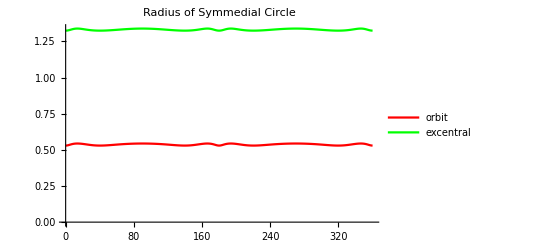

```mathematica
Module[{a=1.5,ell,o,n,s,exc,symCirCtr,symCirRad,symCirCtrExc,symCirRadExc},
ListLinePlot[
Transpose@Table[{o,n,s}=orbitNormals[a,toRad@tDeg];
{symCirCtr,symCirRad}=symmedialCircle[o,s];
exc=excentralTriangle[o,s];
{symCirCtrExc,symCirRadExc}=symmedialCircle[exc,triLengthsRL@exc];
{{tDeg,symCirRad},{tDeg,symCirRadExc}},{tDeg,0,360,1}],PlotStyle->{Red,Green},PlotLegends->{"orbit","excentral"},PlotLabel->"Radius of Symmedial Circle"]]
```

#### And their Ratio is not seem constant

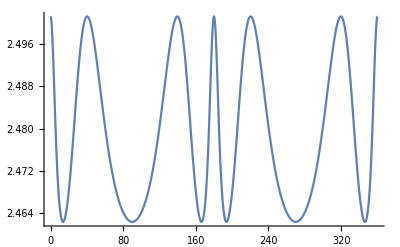

```mathematica
Module[{a=1.5,ell,o,n,s,exc,symCirCtr,symCirRad,symCirCtrExc,symCirRadExc},
Plot[
{o,n,s}=orbitNormals[a,toRad@tDeg];
{symCirCtr,symCirRad}=symmedialCircle[o,s];
exc=excentralTriangle[o,s];
{symCirCtrExc,symCirRadExc}=symmedialCircle[exc,triLengthsRL@exc];
symCirRadExc/symCirRad,{tDeg,0,360}]]
```

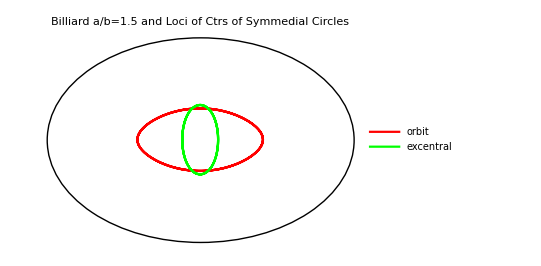

```mathematica
Module[{a=1.5,ell,o,n,s,exc,symCirCtr,symCirRad,symCirCtrExc,symCirRadExc,llp},
ell=plotEll[a,{Thick,Black}];
llp=ListLinePlot[
Transpose@Table[{o,n,s}=orbitNormals[a,toRad@tDeg];
{symCirCtr,symCirRad}=symmedialCircle[o,s];
exc=excentralTriangle[o,s];
{symCirCtrExc,symCirRadExc}=symmedialCircle[exc,triLengthsRL@exc];
{symCirCtr,symCirCtrExc},{tDeg,0,360,1}],PlotStyle->{Red,Green},PlotLegends->{"orbit","excentral"}];
Show[{ell,llp},PlotLabel->"Billiard a/b=1.5 and Loci of Ctrs of Symmedial Circles"]]
```

## Pavage de Billiards (Tilings), Unrolling 3-Periodics

```mathematica
Clear@getOuterPts;getOuterPts[a_?NumericQ,tDeg_?NumericQ]:=Module[{o,n,s,rt2,p3r,n3r,lgt=1,rt3,p1r},
{o,n,s}=orbitNormals[a,toRad@tDeg];
rt2=ReflectionTransform[n[[2]],o[[2]]];
p3r=rt2[o[[3]]];
n3r=rt2[o[[3]]+lgt n[[3]]];
rt3=ReflectionTransform[n3r-p3r,p3r];
p1r=rt3[rt2[o[[1]]]];
{p3r,p1r(*,(o[[1]]+p1r)/2*)}];
```

```mathematica
Clear@show3ells;
Options@show3ells={"max"->8,"lgt"->.4};
show3ells[a_,tDeg_,OptionsPattern[]]:=Module[{o,n,s,gr,ell1,ell2,o3r,ell3,lgt=.4,rt2,s3r,p3r,n3r,rt3,p1r,s1r,lab,L,max,n1r},
lgt=OptionValue@"lgt";
max=OptionValue@"max";
{o,n,s}=orbitNormals[a,toRad@tDeg];
ell1=Graphics[{List@@plotEll[a,{Thick,Black}],Dashed,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}}];
rt2=ReflectionTransform[n[[2]],o[[2]]];
ell2=Graphics[GeometricTransformation[List@@ell1,rt2]];
s3r=GeometricTransformation[Line@{o[[2]],o[[3]]},rt2];
p3r=rt2[o[[3]]];
n3r=rt2[o[[3]]+lgt n[[3]]];
rt3=ReflectionTransform[norm[n3r-p3r],p3r];
p1r=rt3[rt2[o[[1]]]];
n1r=rt3[rt2[o[[1]]+lgt n[[1]]]];
s1r=Line@{p3r,p1r};
ell3=Graphics[GeometricTransformation[List@@ell2,rt3]];
gr=Graphics[{FaceForm@None,PointSize@Large,Arrowheads@Medium,
{MapThread[Arrow[{#1,#1+lgt#2}]&,{o,n}]},
{EdgeForm@{Thick,Blue},Polygon@o,Blue,Point@o,Circle[o[[1]],.075]},
{Thick,Red,s3r},
{Red,Point@p3r,Arrow[{p3r, n3r}]},
{Thick,Darker@Green,s1r,Point@p1r,Arrow[{p1r,n1r}]}}];
L=magn[p1r-o[[1]]];
lab="a="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>", L="<>nfn[L,2];
Show[{ell1,ell2,ell3,gr},PlotLabel->Style[lab,16],ImageSize->Large,PlotRange->{{-max,max},{-max,max}}]]
```

```mathematica
Manipulate[
DynamicModule[{loci},
loci=ListLinePlot[Transpose@Table[getOuterPts[a,tDeg2+.001],{tDeg2,0,360,1}],PlotStyle->{Red,Darker@Green}];
Dynamic[
Show[{show3ells[a,tDeg,"max"->max,"lgt"->(.66 max/8)],loci}]]],
{{a,1.5},1.1,2.,.05},{{tDeg,20},-360,360,1},{{max,8},{1,2,4,8,16}},SaveDefinitions->True]
```

#### Place P1 on origin

```mathematica
Clear@transformParallel;
transformParallel[u_]:=Module[{un=norm@u,ut},
ut=perpNeg[un];
LinearFractionalTransform[{{ut[[1]],ut[[2]],0}, {un[[1]],un[[2]],0},{0,0,1}}]];
```

```mathematica
Clear@getOuterPtsPinP1;
Options@getOuterPtsPinP1={"n1vert"->False,"freezeUp"->False};
getOuterPtsPinP1[a_?NumericQ,tDeg_?NumericQ,OptionsPattern[]]:=Module[{o,n,tr0,tr1d,otr1,otr2,otr3,lgt=.66,trUp,retVal},
{o,n,s}=orbitNormals[a,toRad@tDeg];
tr0=RotationTransform[{n[[1]],{0,1}}];
tr1d=If[OptionValue@"n1vert",
Composition[transformParallel[n[[1]]],TranslationTransform[-o[[1]]]],
TranslationTransform[-o[[1]]]];
otr1=tr1d/@o;(* overwrites, gets back the origin *)
Module[{n2r,tr2d},
n2r=tr1d[o[[2]]+lgt n[[2]]];
tr2d=ReflectionTransform[n2r-otr1[[2]],otr1[[2]]];
otr2=tr2d/@otr1;
Module[{n3r,tr3d},
n3r=tr2d[tr1d[o[[3]]+lgt n[[3]]]];
tr3d=ReflectionTransform[n3r-otr2[[3]],otr2[[3]]];
otr3=tr3d/@otr2;
trUp=transformParallel[otr3[[1]]-otr1[[1]]];
retVal={otr1[[2]],otr2[[3]],otr3[[1]],otr1[[3]],otr2[[1]],otr3[[2]]};
If[OptionValue@"freezeUp",trUp/@retVal,retVal]
]]];
```

```mathematica
Clear@show3ellsPinP1;
Options@show3ellsPinP1={"minY"->-8,"maxY"->8,"minX"->-8,"maxX"->8,"lgt"->.4,"n1vert"->False,"freezeUp"->False};
show3ellsPinP1[a_,tDeg_,OptionsPattern[]]:=Module[{o,n,s,lgt,minX,maxX,minY,maxY,tr1d,otr1,otr2,otr3,gr,ell0,ell1,ell2,ell3,Ltri,Lunr,lab,ntr1,ctr1,R1,ellParam,trUp},
{lgt,minX,maxX,minY,maxY}=OptionValue@{"lgt","minX","maxX","minY","maxY"};
{o,n,s}=orbitNormals[a,toRad@tDeg];
(*tr0=RotationTransform[{n[[1]],{0,1}}];
o1tr0=tr0[o[[1]]];
tr0d=Composition[TranslationTransform[-o1tr0],tr0];*)
tr1d=If[OptionValue@"n1vert",
Composition[transformParallel[n[[1]]],TranslationTransform[-o[[1]]]],
TranslationTransform[-o[[1]]]];
otr1=tr1d/@o;(* overwrites, gets back the origin *)
(*ntr1=MapThread[(tr1d[#1+lgt #2]-tr1d[#1])&,{o,n}];*)
(* plotEll[] is unstable under small motions *)
ellParam=ParametricPlot[{a Cos[t],Sin[t]},{t,0,2π},PlotStyle->{Thick,Gray}];
ell0=Graphics[{List@@ellParam(*plotEll[a,{Thick,Lighter@Gray}]*),{Gray,Dotted,Line@{{-a,0},{a,0}},Line@{{0,-1},{0,1}}},
{FaceForm@None,EdgeForm@{Gray},Polygon@o},
{Arrowheads@Medium,Gray,MapThread[Arrow[{#1,#1+lgt#2}]&,{o,n}]},
{PointSize@Large,MapThread[{#1,Point@#2}&,{{Red,Darker@Green,Blue},o}]}}];
ell1=Graphics[GeometricTransformation[List@@ell0,tr1d]];
Module[{n2r,tr2d},
n2r=tr1d[o[[2]]+lgt n[[2]]];
tr2d=ReflectionTransform[n2r-otr1[[2]],otr1[[2]]];
otr2=tr2d/@otr1;
ell2=Graphics[GeometricTransformation[List@@ell1,tr2d]];
Module[{n3r,tr3d},
n3r=tr2d[tr1d[o[[3]]+lgt n[[3]]]];
tr3d=ReflectionTransform[n3r-otr2[[3]],otr2[[3]]];
otr3=tr3d/@otr2;
ell3=Graphics[GeometricTransformation[List@@ell2,tr3d]]]];
gr=Graphics[{FaceForm@None,PointSize@Large,Arrowheads@Small,
If[OptionValue@"freezeUp",{},{
{Red,Text[Style["P_1",{Bold,18}],otr1[[1]],{0,1.5}],Text[Style["P_1''",{Bold,18}],otr3[[1]],{.5,-1.5}]},
{Darker@Green,Text[Style["P_2",{Bold,18}],otr1[[2]],{-1.5,-.5}]},
{Blue,Text[Style["P_3'",{Bold,18}],otr3[[3]],{1.5,.5}]}}],
{Thick,Black,Line@{otr1[[1]],otr3[[1]]}}
}];
Ltri=Total@s;
Lunr=magn[otr3[[1]]-otr1[[1]]];
(*ctr1=getCircumcenter[otr1[[1]],otr2[[1]],otr3[[1]]];
R1=magn[otr1[[1]]-ctr1];*)
trUp=transformParallel[otr3[[1]]-otr1[[1]]];
lab="a="<>nfn[a,2]<>", θ="<>nfn[tDeg,1]<>", L_tri="<>nfn[Ltri,2]<>", L_unr=" <>nfn[Lunr,2](*<>", R_1="<>nfn[R1,3]*);
Show[If[OptionValue@"freezeUp",Graphics[GeometricTransformation[List@@#,trUp]&/@{ell1,ell2,ell3,gr}],{ell1,ell2,ell3,gr}],PlotLabel->Style[lab,{Black,16}],ImageSize->Large,PlotRange->{{minX,maxX},{minY,maxY}}]]
```

```mathematica
Manipulate[
DynamicModule[{loci},
loci=ListLinePlot[Transpose@Table[getOuterPtsPinP1[1.5,tDeg2+.001,"n1vert"->True],{tDeg2,0,360,1}],PlotStyle->{Darker@Green,Blue,Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
Dynamic[
Show[{show3ellsPinP1[1.5,tDeg,"minX"->-6,"maxX"->2,"minY"->-1,"maxY"->7,"lgt"->.66,"n1vert"->True],loci}]]],
{{tDeg,10.},-360,360,1}]
```

Part::partw: Part 2 of perpNeg[{-1., -0.0000261799}] does not exist.

LinearFractionalTransform::inpf: {{{-1., -0.0000261799}, perpNeg[{-1., -0.0000261799}] ⟦ 2 ⟧, 0}, {-1., -0.0000261799, 0}, {0, 0, 1}} is not a matrix or a list containing a matrix, two vectors, and a scalar.

Part::partw: Part 2 of perpNeg[-LinearFractionalTransform[{{{« 2 »}, Part[« 2 »], 0}, {-1., -0.0000261799, 0}, {0, 0, 1}}][{0., 0.}] + ReflectionTransform[-ReflectionTransform[Plus[« 2 »], LinearFractionalTransform[« 1 »][« 1 »]][LinearFractionalTransform[« 1 »][« 1 »]] + « 1 », « 1 »][« 1 »]/√(-LinearFractionalTransform[{« 3 »}][{« 2 »}] + ReflectionTransform[Times[« 2 »] + ReflectionTransform[« 2 »][« 1 »], ReflectionTransform[Plus[« 2 »], LinearFractionalTransform[« 1 »][« 1 »]][LinearFractionalTransform[« 1 »][« 1 »]]][ReflectionTransform[Plus[« 2 »], « 1 »[« 1 »]][« 1 »]]) . « 1 »] does not exist.

LinearFractionalTransform::inpf: {{{-1., -0.0000261799}, perpNeg[{-1., -0.0000261799}] ⟦ 2 ⟧, 0.}, {-1., -0.0000261799, 0.}, {0., 0., 1.}} is not a matrix or a list containing a matrix, two vectors, and a scalar.

General::stop: Further output of LinearFractionalTransform :: inpf will be suppressed during this calculation.

Part::partw: Part 2 of perpNeg[-1.\ LinearFractionalTransform[{{{« 2 »}, Part[« 2 »], 0.}, {-1., -0.0000261799, 0.}, {0., 0., 1.}}][{0., 0.}] « 1 » ReflectionTransform[-1.\ ReflectionTransform[Plus[« 2 »], LinearFractionalTransform[« 1 »][« 1 »]][« 25 »[« 1 »][« 1 »]] + « 1 »[« 1 »], « 1 »] « 1 » « 1 »]/√(-1.\ LinearFractionalTransform[{« 3 »}][{« 2 »}] + ReflectionTransform[Times[« 2 »] + ReflectionTransform[« 2 »][« 1 »], ReflectionTransform[Plus[« 2 »], LinearFractionalTransform[« 1 »][« 1 »]][LinearFractionalTransform[« 1 »][« 1 »]]][ReflectionTransform[Plus[« 2 »], « 1 »][« 1 »]]) . « 1 »] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], « 43 », getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], « 45 », getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], « 43 », getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], « 45 », getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], « 47 », getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], « 47 », getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], « 47 », getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], « 47 », getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], « 46 », getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], « 46 », getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "n1vert" → True], getOuterPtsPinP1[1.5, 1.001, "n1vert" → True], getOuterPtsPinP1[1.5, 2.001, "n1vert" → True], getOuterPtsPinP1[1.5, 3.001, "n1vert" → True], getOuterPtsPinP1[1.5, 4.001, "n1vert" → True], getOuterPtsPinP1[1.5, 5.001, "n1vert" → True], « 39 », getOuterPtsPinP1[1.5, 45.001, "n1vert" → True], getOuterPtsPinP1[1.5, 46.001, "n1vert" → True], getOuterPtsPinP1[1.5, 47.001, "n1vert" → True], getOuterPtsPinP1[1.5, 48.001, "n1vert" → True], getOuterPtsPinP1[1.5, 49.001, "n1vert" → True], « 311 »}] is not a list of numbers or pairs of numbers.

#### Now with no rotation about N1

```mathematica
Manipulate[
DynamicModule[{loci,lociPts,lociCircs,a=1.5,pts,circ,circGr},
lociPts=Table[getOuterPtsPinP1[a,tDeg2+.001,"freezeUp"->False],{tDeg2,0,360,1}];
loci=ListLinePlot[Transpose@lociPts,PlotStyle->{Darker@Green,Blue,Red,{Dashed,Blue},{Dashed,Red},{Dashed,Darker@Green}}];
lociCircs=ListLinePlot[(getCircumcenter@@Part[#,{4,5,6}])&/@lociPts,PlotStyle->Purple];
Dynamic[
pts=Part[getOuterPtsPinP1[a,tDeg,"freezeUp"->False],{4,5,6}];
circ=getCircumcenter@@pts;
circGr=Graphics@{PointSize@Large,Purple,Point@circ,Dashed,Circle[circ,magn[pts[[1]]-circ]]};
Show[{If[showCirc,{circGr,lociCircs},{}],show3ellsPinP1[1.5,tDeg,"minX"->-8,"maxX"->8,"minY"->-8,"maxY"->8,"lgt"->.66,"freezeUp"->False],loci}]]],
{{tDeg,10.},-360,360,.2},{{showCirc,False},{True,False}}]
```

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], « 44 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], « 44 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 42 », getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], « 43 », getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 46 », getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 46 », getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], « 48 », « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], « 48 », « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], « 44 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 42 », getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], « 43 », getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 2 of perpNeg[{-0.971271, -0.237975}] does not exist.

LinearFractionalTransform::inpf: {{{-0.971271, -0.237975}, perpNeg[{-0.971271, -0.237975}] ⟦ 2 ⟧, 0}, {-0.971271, -0.237975, 0}, {0, 0, 1}} is not a matrix or a list containing a matrix, two vectors, and a scalar.

Part::partw: Part 2 of perpNeg[{-0.964505, -0.264065}] does not exist.

LinearFractionalTransform::inpf: {{{-0.964505, -0.264065}, perpNeg[{-0.964505, -0.264065}] ⟦ 2 ⟧, 0}, {-0.964505, -0.264065, 0}, {0, 0, 1}} is not a matrix or a list containing a matrix, two vectors, and a scalar.

Part::partw: Part 2 of perpNeg[{-0.956598, -0.291411}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

LinearFractionalTransform::inpf: {{{-0.956598, -0.291411}, perpNeg[{-0.956598, -0.291411}] ⟦ 2 ⟧, 0}, {-0.956598, -0.291411, 0}, {0, 0, 1}} is not a matrix or a list containing a matrix, two vectors, and a scalar.

General::stop: Further output of LinearFractionalTransform :: inpf will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], « 44 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], « 44 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], « 47 », getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], « 48 », « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], « 47 », getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], « 48 », « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 46 », getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 46 », getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 46 », getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 46 », getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], « 45 », getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 40 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 5.001, "freezeUp" → False], « 39 », getOuterPtsPinP1[1.5, 45.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 3.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 4.001, "freezeUp" → False], « 41 », getOuterPtsPinP1[1.5, 46.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 47.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 48.001, "freezeUp" → False], getOuterPtsPinP1[1.5, 49.001, "freezeUp" → False], « 311 »}] is not a list of numbers or pairs of numbers.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 0.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 1.001, "freezeUp" → False] does not exist.

Part::partw: Part {4, 5, 6} of getOuterPtsPinP1[1.5, 2.001, "freezeUp" → False] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

### Freeze Unrolled Orbit Upward

```mathematica
Join[{a,b},{c,f}]
```

{a,b,c,f}

```mathematica
Manipulate[
DynamicModule[{a=1.5,lociPts,loci,pts,pts0,lociCircs,circ,ss,inc,gr},
(*
orbit=Reverse@orbit;
sides=Reverse@sides;
getNewCenters[orbit,sides,singles]
*)
lociPts=Table[Drop[getOuterPtsPinP1[a,tDeg2+.001,"freezeUp"->True],3],{tDeg2,0,360,1}];
loci=ListLinePlot[Transpose@lociPts,PlotStyle->{(*Darker@Green,Blue,*){Dashed,Red},{Dashed,Blue},{Dashed,Red}}];
lociCircs=ListLinePlot[(getCircumcenter@@#)&/@lociPts,PlotStyle->Purple];
Dynamic[
(* otr1[[2]],otr2[[3]],otr3[[1]],otr1[[3]],otr2[[1]],otr3[[2]] *)
(* P1 == 0 *)
(* along line: P2, P3', P1'', ragged outers: P3, P1', P2'' *)
pts0=getOuterPtsPinP1[a,tDeg,"freezeUp"->True];
pts=Drop[pts0,3];
circ=getCircumcenter@@pts;
ss=triLengthsRL@pts;
inc=getIncenterTrilin[pts,ss];
gr=Graphics@{PointSize@Large,
{Purple,Point@circ,Dashed,Circle[circ,magn[pts[[1]]-circ]],Orange,Point@inc},MapThread[{#1,Text[Style[#2,{Bold,16}],#3,{-1,-1}]}&,{{Blue,Red,Darker@Green,Purple,Red,Darker@Green,Blue,Red},
{"P_3","P_1'","P_2''","O","P_1","P_2","P_3'","P_1''"},
Join[pts,{circ,{0,0},pts0[[1]],pts0[[2]],pts0[[3]]}]}],
{FaceForm@{Opacity@.1,Yellow},EdgeForm@Gray,Polygon@pts},
{Text["r="<>nfn[getInradius@ss,3],{-1,-1}]}
(* area per not constant *)
(*,
{Text["A="<>nfn[signedArea@pts,3]<>", P="<>nfn[triPer@pts,3],{-1,3}]}*)};
Show[{show3ellsPinP1[a,tDeg,"lgt"->.66,"freezeUp"->True],loci},Epilog->{List@@gr,List@@lociCircs},ImageSize->Medium,PlotRange->{{-3,4},{-1,8}}]]],
{{tDeg,10.},-360,360,.2}]
```

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 34 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 34 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 34 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 34 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 30 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 31 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 39 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 39 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 45 », getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 45 », getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 35 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 36 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 41 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 41 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 29 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 30 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 34 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 34 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 34 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 34 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 43 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 43 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 43 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 43 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 39 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 40 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 39 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 41 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 25 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 24 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »} cannot be transposed.

ListLinePlot::lpn: Transpose[{getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 23 », getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], getOuterPtsPinP1[], « 311 »}] is not a list of numbers or pairs of numbers.